0

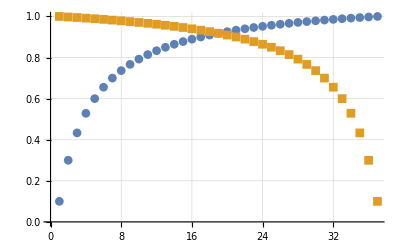

```mathematica
theTime1={(-1/(Range[1,10,.25]))+1.1, (-1/(Range[10,1,-.25]))+1.1};
theDotPos = Array[0&, Length[theTime1]];
theDotPos[[1]]
ListPlot[theTime1, GridLines->Automatic, PlotMarkers->Automatic]
```

```mathematica
Length[theTime1[[2]]]
Length[theTime1[[1]]]
theTime1
```

37

37

{{0.1,0.3,0.433333,0.528571,0.6,0.655556,0.7,0.736364,0.766667,0.792308,0.814286,0.833333,0.85,0.864706,0.877778,0.889474,0.9,0.909524,0.918182,0.926087,0.933333,0.94,0.946154,0.951852,0.957143,0.962069,0.966667,0.970968,0.975,0.978788,0.982353,0.985714,0.988889,0.991892,0.994737,0.997436,1.},{1.,0.997436,0.994737,0.991892,0.988889,0.985714,0.982353,0.978788,0.975,0.970968,0.966667,0.962069,0.957143,0.951852,0.946154,0.94,0.933333,0.926087,0.918182,0.909524,0.9,0.889474,0.877778,0.864706,0.85,0.833333,0.814286,0.792308,0.766667,0.736364,0.7,0.655556,0.6,0.528571,0.433333,0.3,0.1}}

```mathematica
numPositions = Length[theTime1[[1]]] * 2;
theRange = Range[numPositions] (* The coordinate/x-position range to use *)
```

{1,2,3,4,5,6,7,8,9,10,11,12,13,14,15,16,17,18,19,20,21,22,23,24,25,26,27,28,29,30,31,32,33,34,35,36,37,38,39,40,41,42,43,44,45,46,47,48,49,50,51,52,53,54,55,56,57,58,59,60,61,62,63,64,65,66,67,68,69,70,71,72,73,74}

```mathematica
counter = 0;
positions = ConstantArray[0, numPositions];
For[counter = 1, counter < numPositions, counter++,
(
(* TODO: *)
positions[[counter]] = counter * theTime1[[counter]]
)
]
```

Set::noval: Symbol positions in part assignment does not have an immediate value.

Part::partw: Part 3 of {{0.1, 0.3, 0.433333, 0.528571, 0.6, 0.655556, 0.7, 0.736364, 0.766667, 0.792308, 0.814286, 0.833333, 0.85, 0.864706, « 10 », 0.957143, 0.962069, 0.966667, 0.970968, 0.975, 0.978788, 0.982353, 0.985714, 0.988889, 0.991892, 0.994737, 0.997436, 1.}, « 1 »} does not exist.

Set::noval: Symbol positions in part assignment does not have an immediate value.

General::stop: Further output of Set :: noval will be suppressed during this calculation.

Part::partw: Part 4 of {{0.1, 0.3, 0.433333, 0.528571, 0.6, 0.655556, 0.7, 0.736364, 0.766667, 0.792308, 0.814286, 0.833333, 0.85, 0.864706, « 10 », 0.957143, 0.962069, 0.966667, 0.970968, 0.975, 0.978788, 0.982353, 0.985714, 0.988889, 0.991892, 0.994737, 0.997436, 1.}, « 1 »} does not exist.

General::stop: Further output of Part :: partw will be suppressed during this calculation.

```mathematica
ListPlot[positions, GridLines->Automatic, PlotMarkers->Automatic]
```

ListPlot::lpn: positions is not a list of numbers or pairs of numbers.

General::stop: Further output of ListPlot :: lpn will be suppressed during this calculation.

ListPlot[positions,GridLines→Automatic,PlotMarkers→Automatic]